```mathematica
Quit[];
```

```mathematica
testFileName=FileNameJoin[{DirectoryName[NotebookDirectory[],1],FileBaseName[NotebookFileName[]]<>".wlt"}]
pacletDir=DirectoryName[testFileName,2]
If[FileNames[testFileName]==={},Nothing,DeleteFile[testFileName]]
```

```mathematica
Needs["PacletTools`"];
built=PacletBuild[pacletDir]
```

```mathematica
$ContextPath
```

### CI Tests

```mathematica
confirm=False;
```

```mathematica
(*assume tests run when no paclet dependencies are installed*)
Quiet[PacletUninstall["FernandoDuarte/LongRunRisk"]];
Quiet[PacletUninstall["PacletizedResourceFunctions"->"1.0"]];
Quiet[PacletUninstall["MaTeX"->"1.7.9"]];
installed=PacletInstall[built["PacletArchive"]];
$ContextPath=Cases[$ContextPath,Except["PacletizedResourceFunctions`"]];
```

```mathematica
ResourceFunction["WriteUnitTest"][testFileName,
Needs["FernandoDuarte`LongRunRisk`"];
,"ConfirmResults"->confirm]
```

### Interactive Tests

```mathematica
(*when no paclet dependencies are installed*)
Quiet[PacletUninstall["FernandoDuarte/LongRunRisk"]];
Quiet[PacletUninstall["PacletizedResourceFunctions"->"1.0"]];
Quiet[PacletUninstall["MaTeX"->"1.7.9"]];

installed=PacletInstall[built["PacletArchive"]];
Needs["FernandoDuarte`LongRunRisk`"];
And@@(MemberQ[$ContextPath,#]&/@{"FernandoDuarte`LongRunRisk`","MaTeX`","PacletizedResourceFunctions`"})
And@@(MemberQ[Names["FernandoDuarte`LongRunRisk`*"],#]&/@{"Growth","Models"})
And@@(MemberQ[Names["PacletizedResourceFunctions`*"],#]&/@{"NeedsDefinitions","SetSymbolsContext"})
And@@(MemberQ[Names["MaTeX`*"],#]&/@{"MaTeX"})
Models["BY"]["shortname"]=="BY"
Head@MaTeX["x^2"]===Graphics
Not[Information[SetSymbolsContext,"Definitions"]===None]
Not[Information[NeedsDefinitions,"Definitions"]===None]
```

```mathematica
(*when paclet dependencies are already installed*)
Quiet@PacletUninstall["FernandoDuarte/LongRunRisk"];
installed=PacletInstall[built["PacletArchive"]];
Needs["FernandoDuarte`LongRunRisk`"];
And@@(MemberQ[$ContextPath,#]&/@{"FernandoDuarte`LongRunRisk`","MaTeX`","PacletizedResourceFunctions`"})
And@@(MemberQ[Names["FernandoDuarte`LongRunRisk`*"],#]&/@{"Growth","Models"})
And@@(MemberQ[Names["PacletizedResourceFunctions`*"],#]&/@{"NeedsDefinitions","SetSymbolsContext"})
And@@(MemberQ[Names["MaTeX`*"],#]&/@{"MaTeX"})
Models["BY"]["shortname"]=="BY"
Head@MaTeX["x^2"]===Graphics
Not[Information[SetSymbolsContext,"Definitions"]===None]
Not[Information[NeedsDefinitions,"Definitions"]===None]
```

```mathematica
(*when everything is already installed*)
Quiet@PacletUninstall["FernandoDuarte/LongRunRisk"];
installed=PacletInstall[built["PacletArchive"]];
Needs["FernandoDuarte`LongRunRisk`"];
And@@(MemberQ[$ContextPath,#]&/@{"FernandoDuarte`LongRunRisk`","MaTeX`","PacletizedResourceFunctions`"})
And@@(MemberQ[Names["FernandoDuarte`LongRunRisk`*"],#]&/@{"Growth","Models"})
And@@(MemberQ[Names["PacletizedResourceFunctions`*"],#]&/@{"NeedsDefinitions","SetSymbolsContext"})
And@@(MemberQ[Names["MaTeX`*"],#]&/@{"MaTeX"})
Models["BY"]["shortname"]=="BY"
Head@MaTeX["x^2"]===Graphics
Not[Information[SetSymbolsContext,"Definitions"]===None]
Not[Information[NeedsDefinitions,"Definitions"]===None]
```

```mathematica
$ContextPath
```

```mathematica
Needs["FernandoDuarte`LongRunRisk`"]
```

```mathematica
$ContextPath
```

```mathematica
FernandoDuarte`LongRunRisk`Model`Parameters`$parameters
$parameters
```

```mathematica
Models["BY"]["stateVars"]
Short[Models,10]
```

```mathematica
?Models
Keys[Models["BY"]]
```

```mathematica
Complement[model["parameters"],model["assignParam"]]
```

```mathematica
Quiet[PacletUninstall["FernandoDuarte/LongRunRisk"]];
```

```mathematica
Quit[];
```

```mathematica
testFileName=FileNameJoin[{DirectoryName[NotebookDirectory[],1],FileBaseName[NotebookFileName[]]<>".wlt"}];
pacletDir=DirectoryName[testFileName,2];
PacletDirectoryLoad[pacletDir];
testContextBase=FileBaseName[testFileName];
$ContextPath=Cases[$ContextPath,Except["PacletizedResourceFunctions`"]];
```

```mathematica
Get["FernandoDuarte`LongRunRisk`"]
```

```mathematica
Names["Global`*"]
Names["FernandoDuarte`LongRunRisk`*"]
Names["FernandoDuarte`LongRunRisk`Private`*"]
$ContextPath
```

{P0,P1,P2,P4,P5,pacletDir,R0,R1,R2,R4,R5,testContextBase,testFileName}

{Growth,Info,Models,ToExogenous,ToNum,YieldCurve}

{FernandoDuarte`LongRunRisk`Private`args,FernandoDuarte`LongRunRisk`Private`expr,FernandoDuarte`LongRunRisk`Private`expr$,FernandoDuarte`LongRunRisk`Private`model,FernandoDuarte`LongRunRisk`Private`models}

{CodeFormatter`Notebooks`,FernandoDuarte`LongRunRisk`,MaTeX`,PacletizedResourceFunctions`,HighlightingCompatibility`,System`,Global`}

```mathematica
Keys@Models
```

{BY,NRC}

```mathematica
Info[Models]
```

```mathematica
model= Models["BY"];
model["coeffsSolution"]["wc"]//.model["parameters"]//Activate
```

{{{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]→6.24176,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[2]→-470.274}},{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[1]→-(0.333333 (1+ⅇ^(FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0])))/(-1-0.021 ⅇ^(FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]))}}

## Yield Curve

```mathematica
Off[Reduce::ratnz];
```

### BY

```mathematica
myModel = Models["BY"];
```

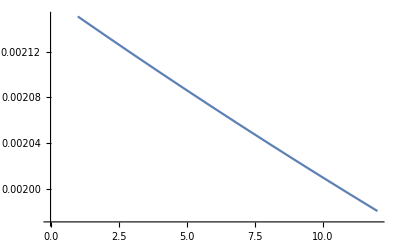

```mathematica
yc=YieldCurve[myModel,{},{}];
ListLinePlot[yc]
```

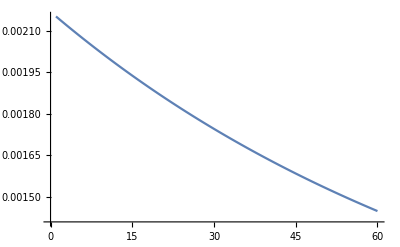

```mathematica
yc=YieldCurve[myModel,{},{},"nombond","MaxMaturity"->60];
ListLinePlot[yc]
```

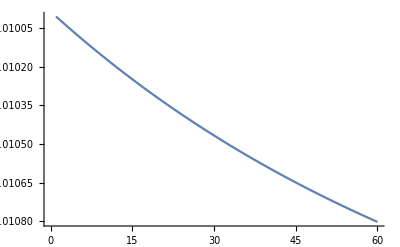

```mathematica
yc=YieldCurve[myModel,{psi->2.1},{},"nombond","MaxMaturity"->60];
ListLinePlot[yc]
```

```mathematica
Manipulate[
ListLinePlot[YieldCurve[myModel,{psi->psiM},{},"nombond","MaxMaturity"->60]]
,{{psiM,2},0.5,3}]
```

### NRC

```mathematica
myModel = Models["NRC"];
```

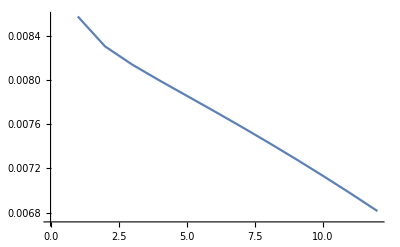

```mathematica
yc=YieldCurve[myModel,{},{}];
ListLinePlot[yc]
```

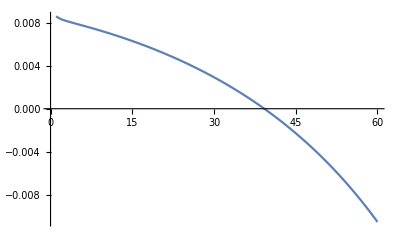

```mathematica
yc=YieldCurve[myModel,{},{},"nombond","MaxMaturity"->60];
ListLinePlot[yc]
```

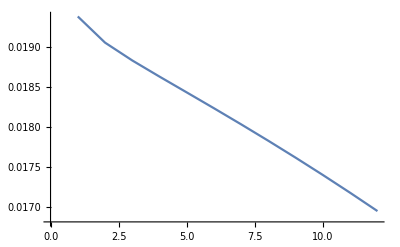

```mathematica
yc=YieldCurve[myModel,{psi->1.8},{},"nombond"];
ListLinePlot[yc]
```

```mathematica
Manipulate[
yc=YieldCurve[myModel,{psi->psiM},{},"nombond","MaxMaturity"->60];
ListLinePlot[yc]
,{{psiM,2},0.5,3}]
```

ReplaceRepeated::reps: {Missing[KeyAbsent,DES][endogenousEq]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»//.Missing[KeyAbsent,DES][assignParamStocks]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Rule::rhs: Pattern FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{{1.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{2.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«7»,{10.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«50»}/.updateCoeffsBond[«1»],Charting`Private`Tag$26717]→({«1»}/.«16»[«1»]).

Rule::rhs: Pattern FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{{1.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{2.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«7»,{10.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«50»}/.updateCoeffsBond[«1»],Charting`Private`Tag$26717]→({«1»}/.«16»[«1»]).

Rule::rhs: Pattern FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{{1.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{2.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«7»,{10.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«50»}/.updateCoeffsBond[«1»],Charting`Private`Tag$26717]→({«1»}/.«16»[«1»]).

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

ListLinePlot::lpn: {{1.,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,1.]//.Missing[KeyAbsent,DES][endogenousEq]/.({«5»}//.Missing[«2»][«1»]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«9»,«50»}/.updateCoeffsBond[Missing[KeyAbsent,DES][coeffsSolution][nombond],«3»,updateCoeffsWc[«1»]] is not a list of numbers or pairs of numbers.

### DES

```mathematica
myModel = Models["DES"];
```

```mathematica
yc=YieldCurve[myModel,{},{}];
ListLinePlot[yc]
```

ReplaceRepeated::reps: {Missing[KeyAbsent,DES][endogenousEq]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»//.Missing[KeyAbsent,DES][assignParamStocks]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {updateCoeffsBond[Missing[KeyAbsent,DES][coeffsSolution][nombond],Missing[KeyAbsent,DES][params],processNewParameters[{},Missing[KeyAbsent,DES][params]],12.,updateCoeffsWc[Missing[KeyAbsent,DES][coeffsSolution][wc],Missing[KeyAbsent,DES][params],processNewParameters[{},Missing[KeyAbsent,DES][params]]]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Missing[KeyAbsent,DES][endogenousEq]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Missing[KeyAbsent,DES][assignParam]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {Missing[KeyAbsent,DES][assignParamStocks]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Rule::rhs: Pattern FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{{1.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{2.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«7»,{10.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«2»}/.updateCoeffsBond[«1»],Charting`Private`Tag$26845]→({«1»}/.«16»[«1»]).

Rule::rhs: Pattern FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{{1.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{2.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«7»,{10.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«2»}/.updateCoeffsBond[«1»],Charting`Private`Tag$26845]→({«1»}/.«16»[«1»]).

Rule::rhs: Pattern FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_ appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,{{1.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{2.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«7»,{10.,ReplaceRepeated[«2»]/.ReplaceRepeated[«2»]//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«2»}/.updateCoeffsBond[«1»],Charting`Private`Tag$26845]→({«1»}/.«16»[«1»]).

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

ListLinePlot::lpn: {{1.,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,1.]//.Missing[KeyAbsent,DES][endogenousEq]/.({«5»}//.Missing[«2»][«1»]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},«9»,«2»}/.updateCoeffsBond[Missing[KeyAbsent,DES][coeffsSolution][nombond],«3»,updateCoeffsWc[«1»]] is not a list of numbers or pairs of numbers.

ListLinePlot[{{1,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,1]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{2,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,2]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{3,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,3]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{4,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,4]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{5,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,5]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{6,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,6]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{7,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,7]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{8,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,8]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{9,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,9]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{10,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,10]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{11,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,11]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]},{12,FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`nombondyield[FernandoDuarte`LongRunRisk`Tools`NicePlots`Private`t,12]//.Missing[KeyAbsent,DES][endogenousEq]/.({_Symbol?(SymbolName[#1]===eps&)[dc][_] _Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>FernandoDuarte`LongRunRisk`Model`Parameters`taugd[FernandoDuarte`LongRunRisk`Model`Shocks`Private`i],_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_]/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>0,_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_]:>0,(_Symbol?(SymbolName[#1]===eps&)[FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$_][_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$_Integer)/;MemberQ[{x,dc,pi,pibar,sg,sx,sc,sp},FernandoDuarte`LongRunRisk`Model`Shocks`Private`var$]:>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p$),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]],(_Symbol?(SymbolName[#1]===eps&)[dd][_,FernandoDuarte`LongRunRisk`Model`Shocks`Private`i_])^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p_Integer):>Expectation[(FernandoDuarte`LongRunRisk`Model`Shocks`Private`y)^(FernandoDuarte`LongRunRisk`Model`Shocks`Private`p),FernandoDuarte`LongRunRisk`Model`Shocks`Private`y\[Distributed]NormalDistribution[0,1]]}//.Missing[KeyAbsent,DES][assignParam]//.Missing[KeyAbsent,DES][assignParamStocks])//.Missing[KeyAbsent,DES][uncondMomOfStateVars]}}/.updateCoeffsBond[Missing[KeyAbsent,DES][coeffsSolution][nombond],Missing[KeyAbsent,DES][params],processNewParameters[{},Missing[KeyAbsent,DES][params]],12,updateCoeffsWc[Missing[KeyAbsent,DES][coeffsSolution][wc],Missing[KeyAbsent,DES][params],processNewParameters[{},Missing[KeyAbsent,DES][params]]]]]

```mathematica
yc=YieldCurve[myModel,{},{},"nombond","MaxMaturity"->60];
ListLinePlot[yc]
```

```mathematica
yc=YieldCurve[myModel,{psi->2.1},{},"nombond","MaxMaturity"->60];
ListLinePlot[yc]
```

```mathematica
Manipulate[
ListLinePlot[Quiet[YieldCurve[myModel,{psi->psiM},{},"nombond","MaxMaturity"->60],Reduce::ratnz]]
,{{psiM,2},0.5,3}]
```

### NRC

```mathematica
myModel = Models["NRC"];
```

```mathematica
yc=YieldCurve[myModel,{},{}];
ListLinePlot[yc]
```

```mathematica
yc=YieldCurve[myModel,{},{},"nombond","MaxMaturity"->60];
ListLinePlot[yc]
```

```mathematica
yc=YieldCurve[myModel,{psi->2.1},{},"nombond","MaxMaturity"->60];
ListLinePlot[yc]
```

```mathematica
Manipulate[
ListLinePlot[YieldCurve[myModel,{psi->psiM},{},"nombond","MaxMaturity"->60]]
,{{psiM,2},0.5,3}]
```

```mathematica
On[Messages Reduce::ratnz]
```

```mathematica
Get["FernandoDuarte`LongRunRisk`Model`ProcessModels`"]
```

```mathematica
model = Models["BY"];
```

```mathematica
cs = model["coeffsSystem"]["wc"];
unknowns=cs[[2]];
coefficientNames=unknowns;
ratioUncondE=model["ratioUncondE"]["wc"];
numStocks = model["numStocks"];
infoModel = model["extraInfo"];

opts
```

opts

```mathematica
FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`createStartingPoint[
coefficientNames,
ratioUncondE,
numStocks,
infoModel
]
```

(Join[{#1},Rest[{{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0],6},{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[1],0},{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[2],0}}]]&)/@If[{}===Cases[Reduce[Simplify[0<FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]<15],FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]],FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014_?NumberQ<FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]<FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014_?NumberQ|FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014_?NumberQ<FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]≤FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014_?NumberQ|FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014_?NumberQ≤FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]<FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014_?NumberQ|FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014_?NumberQ≤FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]≤FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014_?NumberQ:>{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0],If[TrueQ[FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014≤FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`fv$15014≤FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014],FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`fv$15014,(FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014+FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014)/2],FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014,FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014},{0,1}],{{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0],6}},Cases[Reduce[Simplify[0<FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]<15],FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]],FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014_?NumberQ<FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]<FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014_?NumberQ|FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014_?NumberQ<FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]≤FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014_?NumberQ|FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014_?NumberQ≤FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]<FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014_?NumberQ|FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014_?NumberQ≤FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0]≤FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014_?NumberQ:>{FernandoDuarte`LongRunRisk`Model`EndogenousEq`Private`A[0],If[TrueQ[FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014≤FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`fv$15014≤FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014],FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`fv$15014,(FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014+FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014)/2],FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`lb$15014,FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`ub$15014},{0,1}]]

```mathematica
Inactive[Evaluate][Inactive[FilterRules][Inactive[Flatten]@{opts}, Inactive[Options][FindRoot]]],
									Inactive[Evaluate][Inactive[FilterRules][Inactive[Options][addCoeffsSolution], Inactive[Options][FindRoot]]],
									Inactive[Evaluate][Inactive[OptionValue][addCoeffsSolution,"FindRootOptions"]]
```

```mathematica
Inactive[Flatten][{
Inactive[Evaluate][Inactive[FilterRules][Inactive[Flatten]@{opts}, Inactive[Options][RecurrenceTable]]],					Inactive[Evaluate][Inactive[FilterRules][Inactive[Options][addCoeffsSolution], Inactive[Options][RecurrenceTable]]],Inactive[Evaluate][Inactive[OptionValue][addCoeffsSolution,"RecurrenceTableOptions"]]
}]
```